```mathematica
Remove["Global`*"]
<<CompiledFunctionTools`;
<<MaTeX`;
Needs["NumericalCalculus`"]
compileOptions={CompilationTarget->"C",RuntimeOptions->{"EvaluateSymbolically"->False,"CatchMachineUnderflow"->False,"CatchMachineOverflow"->False}};
font={BaseStyle->Directive[FontSize->12],AxesStyle->Directive[FontSize->12],TicksStyle->Directive[FontSize->12],LabelStyle->{FontFamily->"Latin Modern Roman",FontSize-> 12},BaseStyle->texStyle};
```

```mathematica
Get["/home/strelda/Documents/programování/Mathematica/packages/GRQUICK.m"]
```

The convention for this program follow Sean M. Carroll's (Spacetime and Geometry) and the indices run from 0 
to D-1.

While working do not use the variables GARRAY,RARRAY,RsARRAY, CHARRAY, SPEEDOFLIGHT.  

Type ?helpGRQUICK for a list of functions or ?Function for a function description.

More functions and improvements coming soon!!'

# First order perturbation Hamiltonian

```mathematica
$Assumptions={λ∈Reals,χ∈Reals}
```

{λ∈ℝ,χ∈ℝ}

```mathematica
δ[a_,b_]:=KroneckerDelta[a,b];
Je[sn_,j_,m_]:=√((j-sn m)(j+sn m+1));
```

```mathematica
V1[jp_,mp_,j_,m_]:=1/4 δ[jp,j](Je[1,j,m+1]Je[1,j,m]δ[mp,m+2]+Je[-1,j,m-1]Je[-1,j,m]δ[mp,m-2])+δ[jp,j]δ[mp,m](2j(j+1)-2m)
V2[jp_,mp_,j_,m_]:=δ[jp,j](Je[1,j,m]m δ[mp,m+1]+Je[-1,j,m]m δ[mp,m-1]+(m+1)Je[1,j,m]δ[mp,m+1]+(m-1)Je[-1,j,m]δ[mp,m-1]+2j(Je[1,j,m]δ[mp,m+1]+Je[-1,j,m]δ[mp,m-1]))
V3[jp_,mp_,j_,m_]:=δ[jp,j]δ[mp,m](j+m)^2
Hd[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]-λ/(2j)(V1[jp,mp,j,m]+χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m])
```

```mathematica
jj=1;  (*jj=N/2*)
f[mp_,m_]:=Hd[jj,mp,jj,m]
H[λ_,χ_]=Table[f[r,z],{r,-jj,jj},{z,-jj,jj}];
```

```mathematica
If[ConjugateTranspose@H[-3,1]==H[-3,1]/.{λ-> -3,χ->1},Print["Probably is Hermitean"]]
H[λ,χ]//MatrixForm
```

Probably is Hermitean

(-1-3 λ | -(λ χ)/(√2) | -λ/4
-(λ χ)/(√2) | -1/2 λ (4+χ^2) | -(3 λ χ)/(√2)
-λ/4 | -(3 λ χ)/(√2) | 1-1/2 λ (2+4 χ^2))

## Metric tensor

### Metric tensor numerically

```mathematica
DH1[λ_,χ_]=D[H[λ,χ],λ];
DH2[λ_,χ_]=D[H[λ,χ],χ];
gN=Compile[{{λ,_Real},{χ,_Real}},
Module[{g11,g12,g22},
energies=Eigenvalues[H[λ,χ]];
g11=Re@Sum[(DH1[λ,χ][[1,i]])^2/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
g12=Re@Sum[(DH1[λ,χ][[1,i]]DH2[λ,χ][[1,i]])/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
g22=Re@Sum[(DH2[λ,χ][[1,i]])^2/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
{{g11,g12},{g12,g22}}
]]
```

CompiledFunction[…]

#### Metric tensor determinant

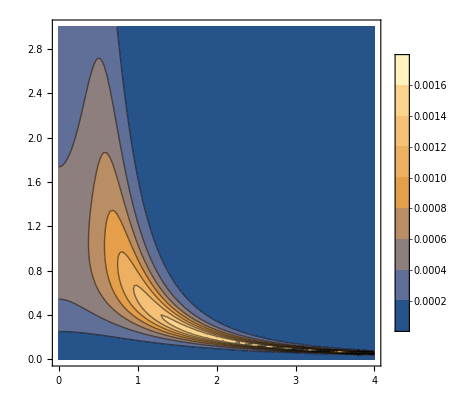

```mathematica
ContourPlot[Det[gN[l,x]],{x,0,4},{l,0,3},PlotRange->Full,PlotLegends->Automatic,PlotPoints->50,FrameLabel->MaTeX/@{"\\chi","\\lambda"},Evaluate@font]
```

### Metric tensor analytically, just pretend we know energies

```mathematica
energies=Eigenvalues[H[λ,0]];
g11=Re@Sum[(DH1[λ,χ][[1,i]])^2/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
g12=Re@Sum[(DH1[λ,χ][[1,i]]DH2[λ,χ][[1,i]])/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
g22=Re@Sum[(DH2[λ,χ][[1,i]])^2/(energies[[1]]-energies[[i]])^2,{i,2,2jj+1}]//FullSimplify;
gS={{g11,g12},{g12,g22}}
```

{{(1+8 χ^2)/(16+λ (32+17 λ)),(8 λ χ)/(16+λ (32+17 λ))},{(8 λ χ)/(16+λ (32+17 λ)),(8 λ^2)/(16+λ (32+17 λ))}}

#### geodesics using GRQUICK

```mathematica
Metin[gS,{λ,χ}]
MatrixForm[GMET]
Einstein[0,0];
Setlight[1];
MatrixForm@Geodesics[τ]
```

Metric Success

((1+8 χ^2)/(16+λ (32+17 λ)) | (8 λ χ)/(16+λ (32+17 λ))
(8 λ χ)/(16+λ (32+17 λ)) | (8 λ^2)/(16+λ (32+17 λ)))

(((16+17 λ[τ]) (-1+8 χ[τ]^2) λ'[τ]^2)/(16+32 λ[τ]+17 λ[τ]^2)+(16 λ[τ] (16+17 λ[τ]) χ[τ] λ'[τ] χ'[τ])/(16+32 λ[τ]+17 λ[τ]^2)+(4 λ[τ]^2 (32+34 λ[τ]) χ'[τ]^2)/(16+λ[τ] (32+17 λ[τ]))+λ''[τ]
-((16+17 λ[τ]) χ[τ] (1+8 χ[τ]^2) λ'[τ]^2)/(λ[τ] (16+32 λ[τ]+17 λ[τ]^2))-(16 (-2+17 λ[τ]^2 χ[τ]^2+2 λ[τ] (-1+8 χ[τ]^2)) λ'[τ] χ'[τ])/(λ[τ] (16+32 λ[τ]+17 λ[τ]^2))-(4 λ[τ] (32+34 λ[τ]) χ[τ] χ'[τ]^2)/(16+λ[τ] (32+17 λ[τ]))+χ''[τ])

```mathematica
init={3,0.5};
vin={1,1};
vinit=vin/(√(-vin.gS.vin))/.{λ->init[[1]],χ->init[[2]]}
MatrixForm[Geodesics[τ]]
Geoplot[τ,init,vinit,{0,10},{λ,χ}]
```

{0.-1.63608 ⅈ,0.-1.63608 ⅈ}

(((16+17 λ[τ]) (-1+8 χ[τ]^2) λ'[τ]^2)/(16+32 λ[τ]+17 λ[τ]^2)+(16 λ[τ] (16+17 λ[τ]) χ[τ] λ'[τ] χ'[τ])/(16+32 λ[τ]+17 λ[τ]^2)+(4 λ[τ]^2 (32+34 λ[τ]) χ'[τ]^2)/(16+λ[τ] (32+17 λ[τ]))+λ''[τ]
-((16+17 λ[τ]) χ[τ] (1+8 χ[τ]^2) λ'[τ]^2)/(λ[τ] (16+32 λ[τ]+17 λ[τ]^2))-(16 (-2+17 λ[τ]^2 χ[τ]^2+2 λ[τ] (-1+8 χ[τ]^2)) λ'[τ] χ'[τ])/(λ[τ] (16+32 λ[τ]+17 λ[τ]^2))-(4 λ[τ] (32+34 λ[τ]) χ[τ] χ'[τ]^2)/(16+λ[τ] (32+17 λ[τ]))+χ''[τ])

{-Graphics-,-Graphics-}

### Metric tensor analytically using stationary perturbation method to find energies

```mathematica
H0d[jp_,mp_,j_,m_]:=m δ[jp,j]δ[mp,m]+λ/(2j)V1[jp,mp,j,m];
Hpd[jp_,mp_,j_,m_]:=λ/(2j)(χ V2[jp,mp,j,m]+χ^2 V3[jp,mp,j,m]);
jj=1;  (*jj=N/2*)
f[mp_,m_]:=H0d[jj,mp,jj,m]
H0[λ_,χ_]=Table[f[r,z],{r,-jj,jj},{z,-jj,jj}];
fp[mp_,m_]:=Hpd[jj,mp,jj,m]
Hp[λ_,χ_]=Table[fp[r,z],{r,-jj,jj},{z,-jj,jj}];
```

```mathematica
N@Eigenvalues[H0[-3,1]]
N@Eigenvalues[Hp[-3,1]]
```

{-10.0697,-6.,-1.93029}

{-10.6439,3.80974,-0.665837}

```mathematica
H0[χ]//MatrixForm
Hp[λ,χ]//MatrixForm
```

(-1 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

(3 | χ/(√2) | 1/4
χ/(√2) | 1/2 (4+χ^2) | (3 χ)/(√2)
1/4 | (3 χ)/(√2) | 1/2 (2+4 χ^2))

```mathematica
e0=Eigenvalues[H0[χ]]
psi0=Eigenvectors[H0[χ]]
```

{-1,1,0}

{{1,0,0},{0,0,1},{0,1,0}}

```mathematica
e1=Conjugate@psi0[[#]].(Hp[λ,χ]. psi0[[#]])&/@Range[1,2jj+1]
e2=Sum[(Conjugate@psi0[[#]].(Hp[λ,χ]. psi0[[#]]))^2/(e0[[#]]-e0[[j]]),{j,DeleteCases[Range[1,2jj+1],#]}]&/@Range[1,2jj+1]
```

{3,1/2 (2+4 χ^2),1/2 (4+χ^2)}

{-27/2,3/8 (2+4 χ^2)^2,0}

```mathematica
en[λ_]:=e0+λ e1+λ^2 e2/.χ->1
```

```mathematica
Det[H[λ,χ]-a IdentityMatrix[2jj+1]]
```

a-a^3+2 λ+2 a λ-6 a^2 λ+4 λ^2-(175 a λ^2)/16-(47 λ^3)/8+(λ χ^2)/2-2 a λ χ^2-5/2 a^2 λ χ^2+λ^2 χ^2-7 a λ^2 χ^2-(7 λ^3 χ^2)/32-λ^2 χ^4-a λ^2 χ^4-2 λ^3 χ^4

# Testing GRQUICK

Metric Success

((2 r'[τ] t'[τ])/((-2+r[τ]) r[τ])+t''[τ]
r'[τ]^2/(2 r[τ]-r[τ]^2)+((-2+r[τ]) t'[τ]^2)/r[τ]^3+(2-r[τ]) θ'[τ]^2-(-2+r[τ]) Sin[θ[τ]]^2 ϕ'[τ]^2+r''[τ]
(2 r'[τ] θ'[τ])/r[τ]-Cos[θ[τ]] Sin[θ[τ]] ϕ'[τ]^2+θ''[τ]
(2 r'[τ] ϕ'[τ])/r[τ]+2 Cot[θ[τ]] θ'[τ] ϕ'[τ]+ϕ''[τ])

1

{√3,0,0,0}

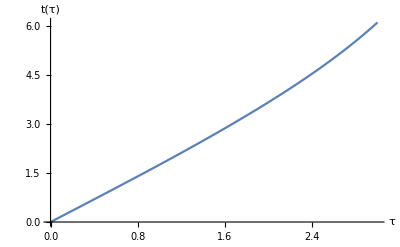
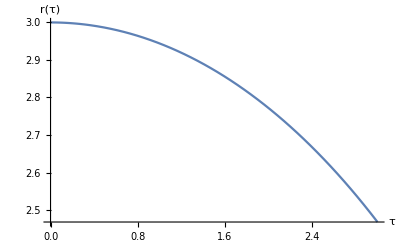

```mathematica
Metin["Schwar"]
MatrixForm[Geodesics[τ]]
Setlight[1];M=1
init={0,3,0,0};
vin={1,0,0,0};
vinit=vin/(√(-vin.GMET.vin))/.{t->init[[1]],r->init[[2]],θ->init[[3]],ϕ->init[[4]]}
Geoplot[τ,init,vinit,{0,3},{t,r}]
```

```mathematica
vinit=vin/(√(vin.GMET.vin))
```

```mathematica
{1/(√(-1+2/r)),0,0,0}/.r->3
```

{-ⅈ √3,0,0,0}

```mathematica
GMET.vin
```

{-1+2/r,0,0,0}